Phonon Modes for Lattice Vibrations with One-Atom Basis

A lattice of atoms can be modelled as harmonic oscillators, with forces proportional to the displacements of the atoms from equilibrium positions.  The simplest such model introduces coupling for only the nearest neighbor atoms.  In this demonstration, a lattice cell containing a single atom is modelled, with nearest neighbor harmonic coupling to the mass in each nearby cell.  Normal mode solutions to these equations of motion are plotted.  Controls are provided to alter the coupling "spring constants" and other free parameters, as well as controls to select from the reciprocal space vectors, and angular frequencies associated with the normal mode solutions.  A time control is also provided to display changes of the lattice through one period of the lattice vibration.

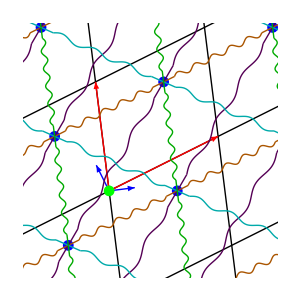

This system of harmonic oscillators, where each mass is coupled to the mass in each of the nearest neighbor cells can be shown to have the form

m OverVector[u^(..)]_n= -k_1∑_± Proj_(â) ((u⃗)_n- (u⃗)_(n ± (1,0)))^2 -k_2∑_± Proj_(b̂) ((u⃗)_n- (u⃗)_(n ± (0, 1)))^2 -k_3∑_± Proj_(r̂) ((u⃗)_n- (u⃗)_(n ± (1, 1)))^2 -k_4∑_± Proj_(ŝ) ((u⃗)_n- (u⃗)_(n ± (1, -1)))^2

Here (u⃗)_nis a vector displacement for the mass in unit cell n from the equilibrium position.  The vectors (r⃗)_(n⃗ = (n_1, n_2)) = n_1 a⃗ + n_2 b⃗ is the position of the n⃗'th unit cell.  The vectors a⃗,b⃗ are the unit cell vectors, defining the equilibrium separation of the masses in the "horizontal", and "vertical" directions.  The vectors r⃗ = b⃗ + a⃗, s⃗ = b⃗ - a⃗ are the  equilibrium separations in the diagonal directions.

A trial solution of the form: (u⃗)_n(r_n', t)= ϵ⃗(q⃗) e^(I (OverVector[r_(n⃗)]. q⃗ - ω t)) can be are used to find to the normal mode solutions of this system, effectively decoupling the equations above, resulting in the eigenvalue problem

(ω^2 | 0
0 | ω^2) ϵ⃗ = 4/m( k_1 â (â)^T sin^2( a⃗ . q⃗/2 ) +  k_2 b̂ (b̂)^T sin^2( b⃗ . q⃗/2 ) +  k_3 r̂ (r̂)^T sin^2( ( b⃗ + a⃗ ). q⃗/2 ) +  k_4 ŝ (ŝ)^T sin^2( ( b⃗ - a⃗ ). q⃗/2 ))ϵ⃗

Here q⃗ is a vector in reciprocal space, effectively parameterizing the angular velocity ω = ω(q⃗).  The vector ϵ⃗(q) is an eigenvector of the equations of motion of the system for this assumed solution, where ω^2 are the eigenvalues of this system.  For this one atom basis, there are two such ω^2 eigenvalues per q⃗ point, each with a different characteristic motion.  A control is available to pick between these two characteristic angular frequencies.

Three tabs are provided in this demonstration.  The primary tab provides plots the solution for particular q⃗ point, and one of the angular velocity eigenvalues for that  q⃗ point.  In that tab, selecting run for the time control will animate the lattice vibrations.  A second tab provides the dispersion relation, the dependence of angular velocity on all  q⃗ points.   Finally, a parameters tab provides controls for the spring constants k_i, and the primitive unit cell lattice vectors a⃗,b⃗.

General theory describing oscillations around the lattice equilibrium points can be found in:

Neil W Ashcroft and N David Mermin. Solid State Physics. Holt, Rinehart and Winston, New York, 1976.  Chapters 21, 22.

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

one atom basis, lattice vibration, phonon, reciprocal lattice vector, angular frequency

Analysis of Lattice Vibrations in Two Dimensions

Motion of Atoms in Crystal

Simple Harmonic Motion for a Spring

Normal Modes in a Periodic Square Lattice

Contributed by: Peeter Joot